# 知識構造化法

2013年度　秋学期、筑波大学　学部3・4年次、5・6限

## 2.データの構造について

### 純関数

```mathematica
f[][3,2]/.{f[]->Function[{x,y},x y]}
```

6

```mathematica
FullForm[f']
```

Derivative[1][f]

```mathematica
FullForm[f'[x]]
```

Derivative[1][f][x]

```mathematica
Derivative[1][x^3][x]
```

(x^3)'[x]

```mathematica
Derivative[1][Function[u,u^3]][x]
```

3 x^2

```mathematica
D[x^3,x]
```

3 x^2

## 4.探索的データ解析

### 正規分布

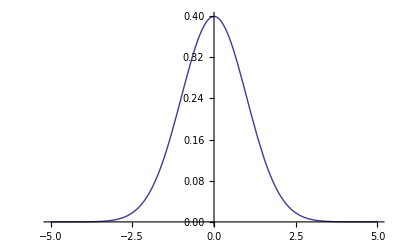

```mathematica
Plot[PDF[NormalDistribution[],m],{m,-5,5}]
```

```mathematica
Integrate[PDF[NormalDistribution[],m],{m,-Infinity,Infinity}]
```

1

## 8.自己組織化マップ

### ニューラルネットワーク

#### ニューロン

加算器

```mathematica
adder[o_List,w_List]:=Tr[w*o]
```

```mathematica
adder[{1,2,3},{a,b,c}]
```

a+2 b+3 c

入出力関数 -シグモイド関数-

```mathematica
SGM[a_,th_]:=1/(1+E^(-a+th))
```

```mathematica
Plot3D[SGM[x,t],{x,-5,5},{t,-14,14}]
```

-Graphics3D-

ニューロンの設計

```mathematica
NER[o_List,w_List,iofunc_,th_]:=If[iofunc[adder[o,w],th]≥th,1,0]
```

```mathematica
ner[o_List,w_List,iofunc_,th_]:=iofunc[adder[o,w],th]
```

#### 教師あり学習

設計したニューロンの性質:

iofuncは、いま、シグモイド(0 < iofunc < 1)に定義されている。
かつ、ニューロンは、いま、非線形活性化関数として機能している。
しきい値 th は、iofunc() そのものにも影響するかたちになっている。

入力を{1,1,1}とする。

thに1以上を設定すると、ニューロンの出力は、かならず 0。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

thに0以下を設定すると、ニューロンの出力は、かならず 1。

```mathematica
Table[{NER[{1,1,1},{-10,-10,-10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

重みをすべて負の値とし、thを0 <= th <= 1の間で変化させる。thが0の場合のみ、ニューロンの出力は1。

```mathematica
Table[{NER[{1,1,1},{-1,-1,-1},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.

重みをすべて大きな正の値とし、thを0 <= th <= 1の間で変化させる。thが1に非常に近い場合にのみ、ニューロンの出力は0。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.

学習データ: {<入力ベクトル>,<期待される出力>}

```mathematica
ldata1={
{{0,0},0},
{{1,0},0},
{{0,1},0},
{{1,1},1}
}
```

{{{0,0},0},{{1,0},0},{{0,1},0},{{1,1},1}}

重みベクトル

```mathematica
wdata1={1.5,-1.}
```

{1.5,-1.}

```mathematica
ldata1[[1, 1]]
```

{0,0}

```mathematica
ner[ldata1[[1,1]],wdata1,SGM,0.1]
```

0.475021

```mathematica
Table[n,{n,0,1,0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
ner[{1,1}, {3,4}, SGM, 0.5]
```

0.998499

```mathematica
Table[{ner[{1,1},{0.5,0.5},SGM,th]-th},{th,0,1,0.1}]
```

{{0.731059},{0.61095},{0.489974},{0.368188},{0.245656},{0.122459},{-0.00131234},{-0.125557},{-0.250166},{-0.375021},{-0.5}}

```mathematica
Table[ner[{1,1},{0.5,0.5},SGM,th],{th,0,1,0.1}]
```

{0.731059,0.71095,0.689974,0.668188,0.645656,0.622459,0.598688,0.574443,0.549834,0.524979,0.5}

```mathematica
NER[ldata1[[1,1]],wdata1,SGM,0.2]
```

1